## B1: First Order

```mathematica
Clear[A,A0];
EqnFirstOrder={
A'[t]==-k A[t],
A[0]==A0
};
FirstOrder = DSolve[EqnFirstOrder,A[t],t][[1]]
A1[t_]=A[t]/.FirstOrder
```

{A[t]→A0 ⅇ^(-k t)}

A0 ⅇ^(-k t)

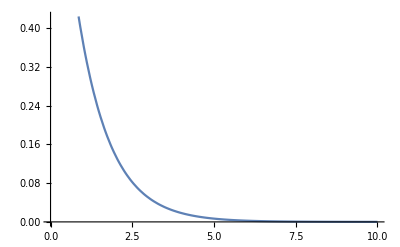

```mathematica
A0Sub = 1;
kSub=1;
Plot[A1[t]/.{A0->A0Sub,k->kSub},{t,0,10}]
```

## B2: Higher Order

```mathematica
Clear[A,A0];
EqnThirdOrder={
A'[t]==-k A[t]^3,
A[0]==A0
};
ThirdOrder=DSolve[EqnThirdOrder,A[t],t][[2]]
(*Index of 2 bc there are two solutions and one is negative, we want the positive one.*)
A3[t_]=A[t]/.ThirdOrder
```

{A[t]→1/(√(1/A0^2+2 k t))}

1/(√(1/A0^2+2 k t))

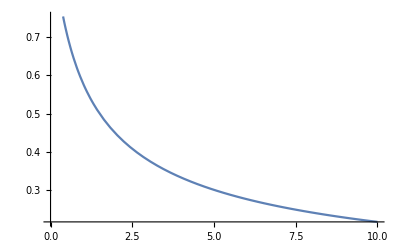

```mathematica
A0Sub = 1;
kSub=1;
Plot[A3[t]/.{A0->A0Sub,k->kSub},{t,0,10}]
```

## B3: Second Order With Two Reactants

```mathematica
(*
The below code gives error because it thinks A[0] and B[0] are variables - why?*)
Clear[A,B,A0,B0];
Eqn={
A'[t]==-k A[t] (B[0]-A[0]+A[t]),
B'[t]==-k A[t] (B[0]-A[0]+A[t]),
A[0]==A0,
B[0]==B0
};
DSolve[Eqn,{A[t],B[t]},t]
```

```mathematica
Clear[A];
secondOrderSol=DSolve[{A'[t]==-k A[t](B0-A0+A[t]),A[0]==A0},A[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{A[t]→((A0-B0) ⅇ^(A0 k t+(B0 (-Log[A0]+Log[B0]))/(A0-B0)))/(-ⅇ^(B0 k t+(A0 (-Log[A0]+Log[B0]))/(A0-B0))+ⅇ^(A0 k t+(B0 (-Log[A0]+Log[B0]))/(A0-B0)))}}

```mathematica
A4[t_]=A[t]/.secondOrderSol/.{B0->2A0}
```

{-(A0 ⅇ^(A0 k t-2 (-Log[A0]+Log[2 A0])))/(-1/2 ⅇ^(2 A0 k t)+ⅇ^(A0 k t-2 (-Log[A0]+Log[2 A0])))}

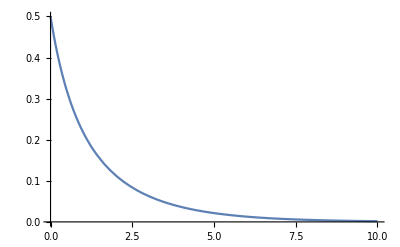

```mathematica
A0Sub = 0.5;
kSub = 1;
Plot[A4[t]/.{A0->A0Sub,k->kSub},{t,0,10},PlotRange->{0,0.5}]
```

```mathematica
(*FOr part b, if we directly substitute into the rate equations and then use DSolve, will it give the same result? The graphs look the same if we do that. But for the case where B0=A0, there is no solution when plugging into the symbolic result but solving with this method gives an answer somehow. ;

Clear[B];
Clear[A];
EqnA={A'[t]==-k A[t](2A0-A0+ A[t])};
Sol = DSolve[{EqnA,A[0]==A0},A[t],t]
*)
```

Note that the value of A0 cannot equal B0 in the solution obtained by DSolve. This is shown by following a similar approach as what was done above.

```mathematica
A5[t_]=A[t]/.secondOrderSol/.{B0->A0}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 A0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 A0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 A0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate}

This is because in that symbolic equation we see that if A0 is plugged into B0, the denominator cancels to 0. The numerator also reduces to 0, causing a result of 0/0 which is indeterminate. Thus, we can say that the mass balance approximation for solving these types of rate equations rely on the assumption that B0 is not equal to A0.

## B4: Reversible First Order

```mathematica
Unprotect[C];
Clear[A,C,kf,kb,A0,C0];
EqnsReversible={
A'[t]==-kf A[t]+kb C[t],
C'[t]==kf A[t]-kb C[t],
A[0]==A0,
C[0]==C0
};
```

```mathematica
SolReversible=DSolve[EqnsReversible,{A[t],C[t]},t][[1]]
```

{A[t]→-(-A0 kb-C0 kb+C0 ⅇ^((-kb-kf) t) kb-A0 ⅇ^((-kb-kf) t) kf)/(kb+kf),C[t]→(C0 ⅇ^((-kb-kf) t) kb+A0 kf+C0 kf-A0 ⅇ^((-kb-kf) t) kf)/(kb+kf)}

```mathematica
Arev[t_]=A[t]/.Part[SolReversible,1]
Crev[t_]=C[t]/.Part[SolReversible,2]
```

-(-A0 kb-C0 kb+C0 ⅇ^((-kb-kf) t) kb-A0 ⅇ^((-kb-kf) t) kf)/(kb+kf)

(C0 ⅇ^((-kb-kf) t) kb+A0 kf+C0 kf-A0 ⅇ^((-kb-kf) t) kf)/(kb+kf)

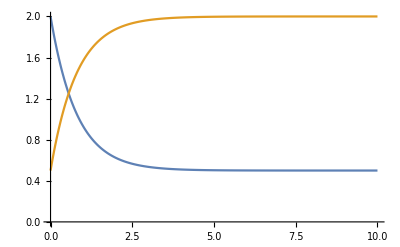

```mathematica
A0Sub=2;
C0Sub=0.5;
kfSub=1;
kbSub=0.25;
Plot[{Arev[t]/.{A0->A0Sub,C0->C0Sub,kf->kfSub,kb->kbSub},Crev[t]/.{A0->A0Sub,C0->C0Sub,kf->kfSub,kb->kbSub}},{t,0,10},PlotRange->{0,2}]
```

```mathematica
EquilConstantFromGraph = 2/0.5
```

4.

```mathematica
EquilConstantFromConstants = kfSub/kbSub
```

4.

The equilibrium constant was calculated using two methods. The first was using the formula Keq=[C]/[A], where the concentrations are those at equilibrium taken from the graph. The second was using the formula Keq=kf/kb. Both methods gave Keq=4, which suggests that the analytical solutions and graph are correct for this reversible first order reaction.

## B5: Sequential Reactions without Back Reactions

```mathematica
Unprotect[C];
Clear[A,B,C,k1,k2,A0,B0,C0];
EqnSeqNB = {
A'[t]==-k1 A[t],
B'[t]==k1 A[t]-k2 B[t],
C'[t]==k2 B[t],
A[0]==A0,
B[0]==B0,
C[0]==C0
};
SolSeqNB = DSolve[EqnSeqNB,{A[t],B[t],C[t]},t][[1]]
```

{A[t]→A0 ⅇ^(-k1 t),B[t]→(ⅇ^(-k1 t-k2 t) (-A0 ⅇ^(k1 t) k1-B0 ⅇ^(k1 t) k1+A0 ⅇ^(k2 t) k1+B0 ⅇ^(k1 t) k2))/(-k1+k2),C[t]→1/(-k1+k2)ⅇ^(-k1 t-k2 t) (A0 ⅇ^(k1 t) k1+B0 ⅇ^(k1 t) k1-A0 ⅇ^(k1 t+k2 t) k1-B0 ⅇ^(k1 t+k2 t) k1-C0 ⅇ^(k1 t+k2 t) k1-B0 ⅇ^(k1 t) k2-A0 ⅇ^(k2 t) k2+A0 ⅇ^(k1 t+k2 t) k2+B0 ⅇ^(k1 t+k2 t) k2+C0 ⅇ^(k1 t+k2 t) k2)}

```mathematica
AseqNB[t_]=A[t]/.Part[SolSeqNB,1]/.{A0->1,B0->0,C0->0}
BseqNB[t_]=B[t]/.Part[SolSeqNB,2]/.{A0->1,B0->0,C0->0}
CseqNB[t_]=C[t]/.Part[SolSeqNB,3]/.{A0->1,B0->0,C0->0}
```

ⅇ^(-k1 t)

(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t) k1+ⅇ^(k2 t) k1))/(-k1+k2)

(ⅇ^(-k1 t-k2 t) (ⅇ^(k1 t) k1-ⅇ^(k1 t+k2 t) k1-ⅇ^(k2 t) k2+ⅇ^(k1 t+k2 t) k2))/(-k1+k2)

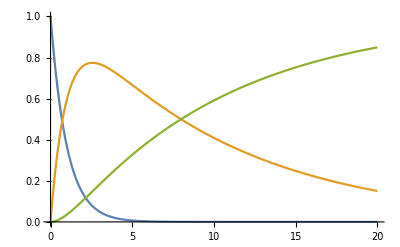

```mathematica
k1Sub=1;
k2Sub=0.1;
Plot[{AseqNB[t]/.{k1->k1Sub,k2->k2Sub},BseqNB[t]/.{k1->k1Sub,k2->k2Sub},CseqNB[t]/.{k1->k1Sub,k2->k2Sub}},{t,0,20}]
```

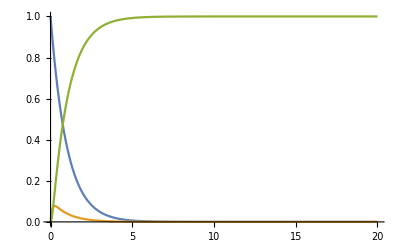

```mathematica
k1Sub=1;
k2Sub=10;
Plot[{AseqNB[t]/.{k1->k1Sub,k2->k2Sub},BseqNB[t]/.{k1->k1Sub,k2->k2Sub},CseqNB[t]/.{k1->k1Sub,k2->k2Sub}},{t,0,20}]
```

When the value of k2 is 10, the concentration of B barely builds up and instead depletes very rapidly as it quickly reacts to produce C. On the other hand, for a k2 value of 0.1, there was a large build up of B before it was able to slowly react and produce a higher amount of C than B. Thus, if we see a large concentration of the intermediate B building up at an intermediate time, that implies that the value of the rate constant k2 is small compared to k1. If there is minimal buildup of B, that implies that the value of k2 is large compared to k1.

## B6: Sequential Reactions with Back Reactions

```mathematica
Unprotect[C];
Clear[A,B,C,k1,k2,k1b,k2b,A0,B0,C0];
EqnSeqB={
A'[t]==-k1 A[t] + k1b B[t],
B'[t]==k1 A[t]-k1b B[t]-k2 B[t]+k2b C[t],
C'[t]==k2 B[t]-k2b C[t],
A[0]==A0,
B[0]==B0,
C[0]==C0
};
SolSeqB=DSolve[EqnSeqB,{A[t],B[t],C[t]},t][[1]];
```

```mathematica
AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->1,B0->0,C0->0,k1->1,k2->0.1,k1b->0.05,k2b->0.1}
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->1,B0->0,C0->0,k1->1,k2->0.1,k1b->0.05,k2b->0.1}
CseqB[t_]=C[t]/.Part[SolSeqB,3]/.{A0->1,B0->0,C0->0,k1->1,k2->0.1,k1b->0.05,k2b->0.1}
```

-3.28488 (-0.007425-0.28637 ⅇ^(-1.05584 t)-0.0106305 ⅇ^(-0.194158 t))

-3.28488 (-0.1485+0.31983 ⅇ^(-1.05584 t)-0.17133 ⅇ^(-0.194158 t))

-3.28488 (-0.1485-0.0334605 ⅇ^(-1.05584 t)+0.181961 ⅇ^(-0.194158 t))

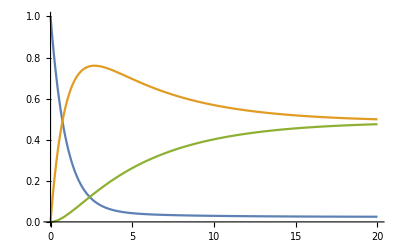

```mathematica
Plot[{AseqB[t],BseqB[t],CseqB[t]},{t,0,20}]
```

Compared to the case where back reactions were neglected, the equilibrium concentrations in this case are different. The concentration of B stays higher than the concentration of C for a longer period of time, whereas when the back reaction was neglected, the concentration of B quickly crossed below the concentration of C. This is because it was assumed that C was not reacting backwards at all to produce B, such that the concentration of B was only being depleted by the forward reaction. The previous assumptions were thus only valid up to a time of about 8.

-0.144676 (-3.456-2.1983 ⅇ^(-3.06969 t)-1.2577 ⅇ^(-0.130306 t))

-0.144676 (-1.728+2.27491 ⅇ^(-3.06969 t)-0.546906 ⅇ^(-0.130306 t))

-0.144676 (-1.728-0.0766041 ⅇ^(-3.06969 t)+1.8046 ⅇ^(-0.130306 t))

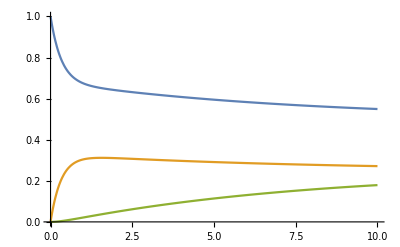

```mathematica
AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->1,B0->0,C0->0,k1->1,k2->0.1,k1b->2,k2b->0.1}
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->1,B0->0,C0->0,k1->1,k2->0.1,k1b->2,k2b->0.1}
CseqB[t_]=C[t]/.Part[SolSeqB,3]/.{A0->1,B0->0,C0->0,k1->1,k2->0.1,k1b->2,k2b->0.1}

Plot[{AseqB[t],BseqB[t],CseqB[t]},{t,0,10}]
```

## B7: Steady State Approximation

```mathematica
Unprotect[C];
(*
B'[t]=k1 A[t] - k1b B[t] - k2  B[t] + k2b C[t] = 0;
k2 B[t] + k1 B[t] = k1 A[t] +k2b C[t];
B[t](k2+k1b) = k1 A[t]+k2b C[t];
B[t]= (k1 A[t]+k2b C[t])/(k2+k1b);
*)

Clear[A,B,C,k1,k1b,k2,k2b,A0,B0,C0]
BtSub = Solve[k1 A[t] - k1b B[t] - k2  B[t] + k2b C[t] == 0, B[t]][[1]]
```

{B[t]→(k1 A[t]+k2b C[t])/(k1b+k2)}

```mathematica
EqnSSA={
A'[t]==-k1 A[t] + k1b (B[t]/.BtSub),
C'[t]==k2 (B[t]/.BtSub)-k2b C[t],
A[0]==A0,
C[0]==C0
};
SolSeqBSS=DSolve[EqnSSA, {A[t],C[t]},t][[1]]
```

{A[t]→(A0 ⅇ^(((-k1 k2-k1b k2b) t)/(k1b+k2)) k1 k2+A0 k1b k2b+C0 k1b k2b-C0 ⅇ^(((-k1 k2-k1b k2b) t)/(k1b+k2)) k1b k2b)/(k1 k2+k1b k2b),C[t]→-(-A0 k1 k2-C0 k1 k2+A0 ⅇ^(((-k1 k2-k1b k2b) t)/(k1b+k2)) k1 k2-C0 ⅇ^(((-k1 k2-k1b k2b) t)/(k1b+k2)) k1b k2b)/(k1 k2+k1b k2b)}

-3.28488 (-0.007425-0.28637 ⅇ^(-1.05584 t)-0.0106305 ⅇ^(-0.194158 t))

-3.28488 (-0.1485-0.0334605 ⅇ^(-1.05584 t)+0.181961 ⅇ^(-0.194158 t))

9.52381 (0.005+0.1 ⅇ^(-0.7 t))

-9.52381 (-0.1+0.1 ⅇ^(-0.7 t))

Exact:

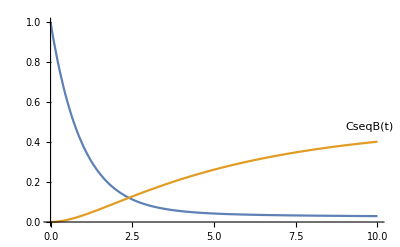

Using Steady State Approximation:

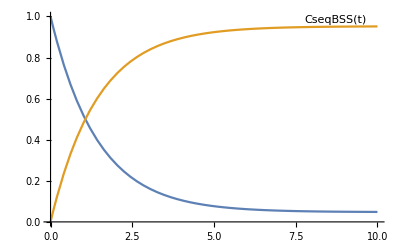

```mathematica
A0Sub=1;
B0Sub=0;
C0Sub=0;
k1Sub=1;
k2Sub=0.1;
k1bSub=0.05;
k2bSub=0.1;

(*Sequential with back reaction, exact*)

AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqB[t_]=C[t]/.Part[SolSeqB,3]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}

(*Sequential with back reaction, steady state approximation*)

AseqBSS[t_]=A[t]/.Part[SolSeqBSS,1]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqBSS[t_]=C[t]/.Part[SolSeqBSS,2]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}

Print["Exact:"]
Plot[{AseqB[t],CseqB[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]

Print["Using Steady State Approximation:"]
Plot[{AseqBSS[t],CseqBSS[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]
```

-4.41575 (-0.0030603-0.07878 ⅇ^(-1.11 t)-0.0313908 ⅇ^(-0.1 t))

-4.41575 (-0.30603-0.007878 ⅇ^(-1.11 t)+0.313908 ⅇ^(-0.1 t))

-4.41575 (-0.030603+0.086658 ⅇ^(-1.11 t)-0.282517 ⅇ^(-0.1 t))

9.90099 (0.0005+0.05 ⅇ^(-0.505 t))

-9.90099 (-0.05+0.05 ⅇ^(-0.505 t))

5. (-0.0990099 (-0.05+0.05 ⅇ^(-0.505 t))+9.90099 (0.0005+0.05 ⅇ^(-0.505 t)))

Exact:

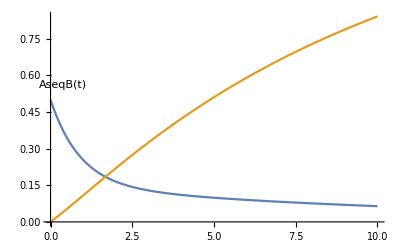

Using Steady State Approximation:

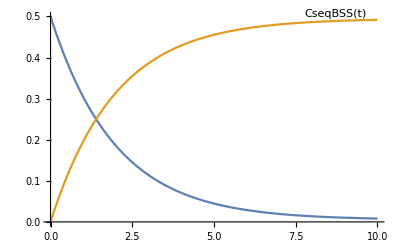

```mathematica
A0Sub=0.5;
B0Sub=1;
C0Sub=0;
k1Sub=1;
k2Sub=0.1;
k1bSub=0.1;
k2bSub=0.01;


AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqB[t_]=C[t]/.Part[SolSeqB,3]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}

AseqBSS[t_]=A[t]/.Part[SolSeqBSS,1]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqBSS[t_]=C[t]/.Part[SolSeqBSS,2]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
BseqBSS[t_]=B[t]/.BtSub/.{k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub, A[t]->AseqBSS[t],C[t]->CseqBSS[t]}

Print["Exact:"]
Plot[{AseqB[t],CseqB[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]

Print["Using Steady State Approximation:"]
Plot[{AseqBSS[t],CseqBSS[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]
```

-3.38753 (-0.05535-0.240464 ⅇ^(-1.10523 t)+0.000613814 ⅇ^(-0.144766 t))

-3.38753 (-0.27675-0.0125866 ⅇ^(-1.10523 t)-0.00586336 ⅇ^(-0.144766 t))

-3.38753 (-0.5535+0.25305 ⅇ^(-1.10523 t)+0.00524955 ⅇ^(-0.144766 t))

16.6667 (0.02+0.04 ⅇ^(-0.4 t))

-16.6667 (-0.1+0.04 ⅇ^(-0.4 t))

6.66667 (-1.66667 (-0.1+0.04 ⅇ^(-0.4 t))+16.6667 (0.02+0.04 ⅇ^(-0.4 t)))

Exact:

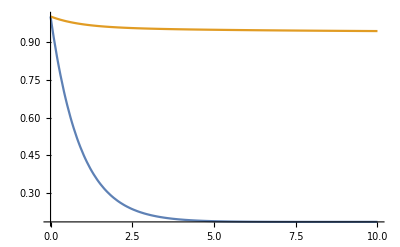

Using Steady State Approximation:

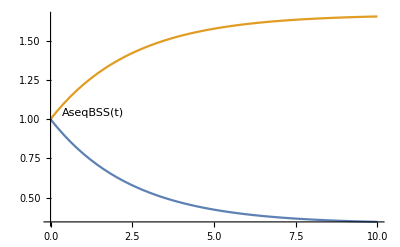

```mathematica
A0Sub=1;
B0Sub=1;
C0Sub=1;
k1Sub=1;
k2Sub=0.05;
k1bSub=0.1;
k2bSub=0.1;


AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqB[t_]=C[t]/.Part[SolSeqB,3]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}

AseqBSS[t_]=A[t]/.Part[SolSeqBSS,1]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqBSS[t_]=C[t]/.Part[SolSeqBSS,2]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
BseqBSS[t_]=B[t]/.BtSub/.{k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub, A[t]->AseqBSS[t],C[t]->CseqBSS[t]}

Print["Exact:"]
Plot[{AseqB[t],CseqB[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]

Print["Using Steady State Approximation:"]
Plot[{AseqBSS[t],CseqBSS[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]
```

The steady state approximation works better when the initial concentration of C is 0, as opposed to the case above. If C0 is not 0 like this case, the results are especially off in the time interval of about 0 to 4. For the previous cases, the results were especially off for the time interval of large t values, with greater and greater error the more that t increased to infinity.

-2.65252 (-0.0435-0.123659 ⅇ^(-1.11926 t)-0.0213409 ⅇ^(-0.580742 t))

-2.65252 (-0.087-0.0238146 ⅇ^(-1.11926 t)+0.110815 ⅇ^(-0.580742 t))

-2.65252 (-0.435+0.147474 ⅇ^(-1.11926 t)-0.0894736 ⅇ^(-0.580742 t))

6.66667 (0.025+0.05 ⅇ^(-0.75 t))

-6.66667 (-0.05+0.05 ⅇ^(-0.75 t))

5. (-3.33333 (-0.05+0.05 ⅇ^(-0.75 t))+6.66667 (0.025+0.05 ⅇ^(-0.75 t)))

Exact:

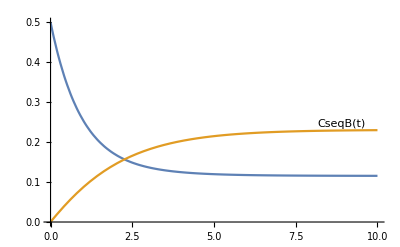

Using Steady State Approximation:

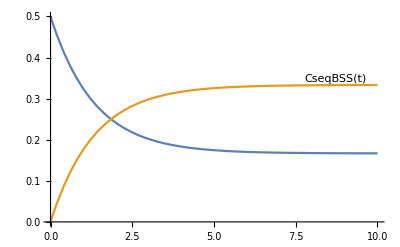

```mathematica
A0Sub=0.5;
B0Sub=1;
C0Sub=0;
k1Sub=1;
k2Sub=0.1;
k1bSub=0.1;
k2bSub=0.5;


AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqB[t_]=C[t]/.Part[SolSeqB,3]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->A0Sub,B0->B0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}

AseqBSS[t_]=A[t]/.Part[SolSeqBSS,1]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
CseqBSS[t_]=C[t]/.Part[SolSeqBSS,2]/.{A0->A0Sub,C0->C0Sub,k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub}
BseqBSS[t_]=B[t]/.BtSub/.{k1->k1Sub,k2->k2Sub,k1b->k1bSub,k2b->k2bSub, A[t]->AseqBSS[t],C[t]->CseqBSS[t]}

Print["Exact:"]
Plot[{AseqB[t],CseqB[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]

Print["Using Steady State Approximation:"]
Plot[{AseqBSS[t],CseqBSS[t]},{t,0,10},PlotLabels->Placed[Automatic,Above]]
```

This final case produced the graphs that look the most similar compared to all the trials. What was distinct about this last trials is that the value of k2b was larger, along with a C0 of 0. The approximation is not as good in the starting